```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/IXS2/IXS/IXS

## Anomalous mass dimension

```mathematica
gam={
1,
1/16(202/3-20/9nf),
1/64(1249+(-2216/27-160/3Zeta[3])nf-140/81nf^2),
1/256(4603055/162+135680/27Zeta[3]-8800 Zeta[5]+(-91723/27-34192/9Zeta[3]+880Zeta[4]+18400/9Zeta[5])nf
+(5242/243+800/9Zeta[3]-160/3Zeta[4])nf^2+(-332/243+62/27Zeta[3])nf^3)
}
```

{1,1/16 (202/3-(20 nf)/9),1/64 (1249-(140 nf^2)/81+nf (-2216/27-(160 Zeta[3])/3)),1/256 (4603055/162+(135680 Zeta[3])/27+nf^3 (-332/243+(62 Zeta[3])/27)+nf^2 (5242/243-(16 π^4)/27+(800 Zeta[3])/9)-8800 Zeta[5]+nf (-91723/27+(88 π^4)/9-(34192 Zeta[3])/9+(18400 Zeta[5])/9))}

```mathematica
gam//N//Expand//TableForm
```

1.
4.20833-0.138889 nf
19.5156-2.28412 nf-0.0270062 nf^2
98.9434-19.1075 nf+0.276163 nf^2+0.0054454 nf^3

```mathematica
gam//N//Expand//CForm
```

List(1.,4.208333333333333 - 0.1388888888888889*nf,19.515625 - 2.284121493373736*nf - 0.02700617283950617*Power(nf,2),
   98.9434142552029 - 19.1074619186354*nf + 0.27616255142989465*Power(nf,2) + 0.005445404963397852*Power(nf,3))

```mathematica
Log[2]2//N
```

1.38629

```mathematica
del=1124.3088874944671+L*316.33715474767372-L^2*746.75594726351075+L^3*143.2983223337546/.L->N[Log[2]2,16]
N[%,20]
```

509.496

509.496

```mathematica
15.05431790437694*0.1251607211653761^3/π^3 509.496
```

0.485016

## Coefficient Functions

```mathematica
Get["Distributions/CoefficientFunctions.txt"];
```

```mathematica
allcoefs={ggcoef,qgcoef,qqbarcoef,qqcoef,qQ2coef};
%//Dimensions
```

{5,1000}

```mathematica
funcs=Table[Table[{N[j/1000],allcoefs[[i,j]]},{j,1,999}],{i,1,Length[allcoefs]}];
```

```mathematica
Export["~/Desktop/CoefficientFunctions.txt",ToString[InputForm[funcs]]]
```

~/Desktop/CoefficientFunctions.txt

```mathematica
KK=1.06274;
```

```mathematica
15.9988/KK
36.8376/KK
46.3987/KK
47.895/KK
```

15.0543

34.6629

43.6595

45.0675

```mathematica
2(46.3987/KK-43.6601)/(46.3987/KK+43.6601) 100
2(47.895/KK-45.0722)/(47.895/KK+45.0722) 100
```

-0.00136786

-0.0105012

```mathematica
9.21813-4.29572+5.81404+7.46067
3.08856-3.90674+0.10790+1.63478-4.75985+8.01313+3.93638
0.30444+0.48416
0.00493+0.00664
```

18.1971

8.11416

0.7886

0.01157

```mathematica
0.90011-0.06430+0.34161+0.09498-5.55239-5.47960+0.86254-9.14402+18.98918+0.49967
0.01769+0.10609-0.12262
2.86430 10^-4+0.00145+0.00786
0.00475+0.00686
0.01319+0.02551
```

1.44778

0.00116

0.00959643

0.01161

0.0387

```mathematica
45.0704KK
```

47.8981

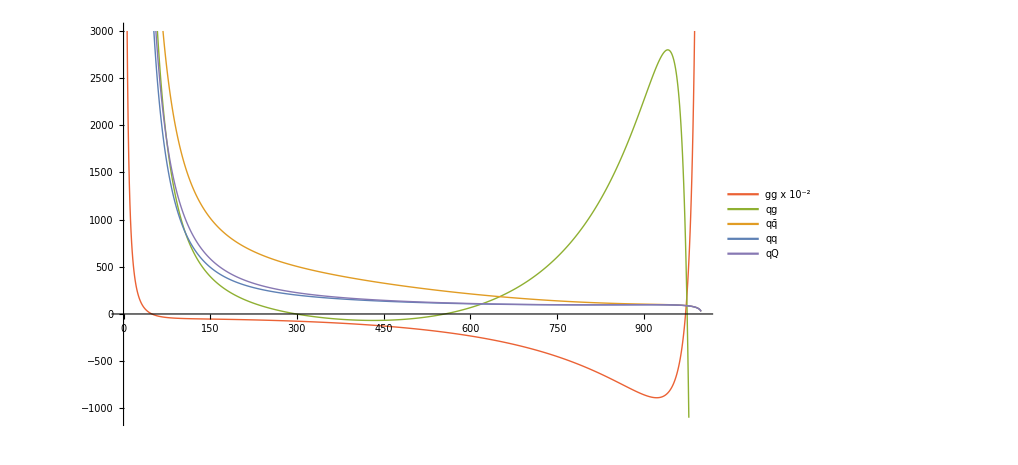

```mathematica
pp=ListLinePlot[{ggcoef/100,qgcoef,qqbarcoef,qqcoef,qQ2coef},
PlotStyle->{
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[5]],Thick},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]],Thin},
{ColorData[97,"ColorList"][[4]],Thin}
},
PlotLegends->Placed[LineLegend[{"gg x 10^-2 ","qg\t","qq̄\t","qq\t","qQ"},LegendLayout->{"Row",3}],{0.5,0.69}],
PlotRange->{-1100,3000}]
```

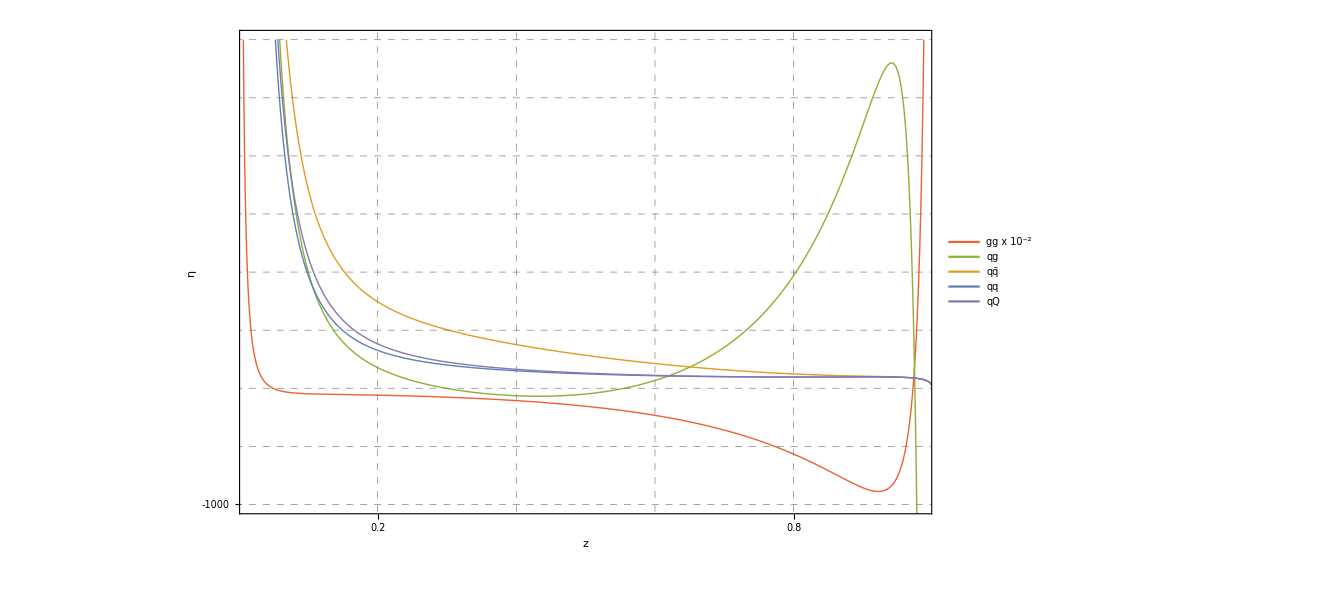

```mathematica
ppp=Show[pp,
PlotRange->{{20,980},{-1000,3000}},
Frame->True,
FrameTicks->{Table[{i,i/200/5//N} 200,{i,-20,20}],500Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i 200,{i,-10,10}],Table[500 i,{i,-10,12}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" z","η"},
LabelStyle->Directive[Bold,20]
]
```

## Scale Variation

```mathematica
vars=StringReplace[Import["Distributions/ScaleVariations_PDF4LHC.txt"],{"e-"->"*10^-"}]//ToExpression;
```

```mathematica
LO=vars[[;;,1,1]]+vars[[;;,2,1]]+vars[[;;,3,1]]+vars[[;;,4,1]]+vars[[;;,5,1]];
NLO=LO+vars[[;;,1,2]]+vars[[;;,2,2]]+vars[[;;,3,2]]+vars[[;;,4,2]]+vars[[;;,5,2]];
NNLO=NLO+vars[[;;,1,3]]+vars[[;;,2,3]]+vars[[;;,3,3]]+vars[[;;,4,3]]+vars[[;;,5,3]];
N3LO=NNLO+vars[[;;,1,4]]+vars[[;;,2,4]]+vars[[;;,3,4]]+vars[[;;,4,4]]+vars[[;;,5,4]];
```

```mathematica
extreme={{42,45.4924},{62.5,45.1805},{125,43.6962}};
(extreme[[1,2]]-extreme[[2,2]])
(extreme[[3,2]]-extreme[[2,2]])
2(extreme[[1,2]]-extreme[[2,2]])/(extreme[[1,2]]+extreme[[2,2]])100
2(extreme[[3,2]]-extreme[[2,2]])/(extreme[[3,2]]+extreme[[2,2]])100
```

0.3119

-1.4843

```mathematica
thmax=45.3292;
thmin=43.6348;
thcent=45.0684;
thmax-thcent
thmin-thcent
2(thmax-thcent)/(thmax+thcent)100
2(thmin-thcent)/(thmin+thcent)100
```

0.2608

-1.4336

0.577006

-3.23235

```mathematica
45.1805
```

```mathematica
0.248256-0.122586+0.00785785+0.00686339+0.025381
```

0.165772

```mathematica
scales[[20]]
```

125

```mathematica
vars[[;;20,;;,4]]
```

{{-2.32372,-0.339668,0.0210109,0.0268008,0.0781365},{-1.54526,-0.0670449,0.0173538,0.0229113,0.0687463},{-0.851964,0.0621997,0.0147172,0.019683,0.0601793},{-0.23532,0.110052,0.0128213,0.0170916,0.0530733},{0.315673,0.108617,0.011465,0.0150358,0.0474346},{0.810005,0.0782449,0.0105066,0.0134171,0.0430969},{1.25558,0.0303516,0.00984253,0.0121441,0.0398437},{1.66015,-0.0288711,0.00940279,0.0111517,0.0374954},{2.02944,-0.0951489,0.00913369,0.0103838,0.0358865},{2.36818,-0.165773,0.00899544,0.00979655,0.0348796},{2.68028,-0.238296,0.00895905,0.0093563,0.0343662},{2.96896,-0.311399,0.00900216,0.00903604,0.0342564},{3.23682,-0.384426,0.00910762,0.00881423,0.0344772},{3.48642,-0.456601,0.00926224,0.00867333,0.0349696},{3.71967,-0.52773,0.0094555,0.00859953,0.035685},{3.93826,-0.597435,0.00967919,0.00858142,0.0365836},{4.14364,-0.665569,0.0099268,0.00860948,0.0376326},{4.33714,-0.732044,0.0101931,0.00867657,0.0388055},{4.51983,-0.796818,0.0104739,0.00877613,0.0400798},{4.69268,-0.859794,0.0107658,0.00890285,0.0414365}}

```mathematica
N3LO
```

{45.2184,45.4207,45.489,45.4796,45.423,45.3384,45.236,45.123,45.0036,44.8802,44.7556,44.6313,44.5072,44.385,44.2645,44.1461,44.03,43.9161,43.8049,43.6961,43.5896,43.4858,43.3838,43.2842,43.1869,43.092,42.9991,42.9083,42.8194,42.7323,42.6471,42.5637,42.482,42.4019,42.3234,42.2467,42.1711,42.0972,42.0216,41.9508,41.8808,41.8149,41.7475,41.6811,41.6115}

```mathematica
scales=Table[25+ 5 i,{i,1,45}]
```

{30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250}

```mathematica
N3LO//Length
```

45

```mathematica
Abs[vars[[;;,1,4]]+vars[[;;,2,4]]+vars[[;;,3,4]]+vars[[;;,4,4]]+vars[[;;,5,4]]]
Min[%]
25+5 Position[%%,%][[1,1]]
```

{2.53744,1.50329,0.695185,0.0422823,0.498226,0.955271,1.34776,1.68933,1.9897,2.25607,2.49467,2.70985,2.90479,3.08272,3.24568,3.39567,3.53424,3.66277,3.78234,3.89399,3.99842,4.09645,4.18853,4.27532,4.3573,4.43489,4.50842,4.57821,4.64457,4.70774,4.76797,4.82549,4.88044,4.93305,4.98344,5.03185,5.07817,5.12278,5.16447,5.20591,5.24563,5.28512,5.32211,5.35781,5.39049}

0.0422823

45

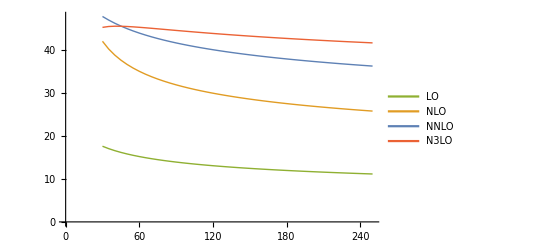

```mathematica
pp=ListLinePlot[Transpose[{Table[scales[[i]],{i,1,Length[scales]}],#}]&/@
({LO,
NLO,
NNLO,
N3LO
})

,PlotStyle->{{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"LO\t     ","NLO\t","NNLO\t","N3LO\t"},LegendLayout->{"Row",2}],{0.6,0.15}]
]
```

```mathematica
LabelStyle->Directive[Bold,20]
```

LabelStyle→Directive[Bold,20]

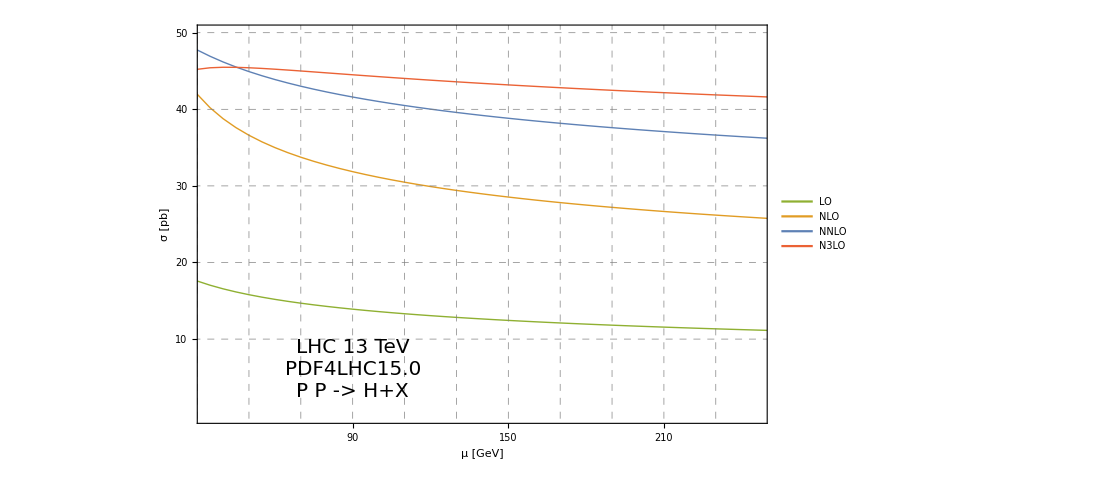

```mathematica
Show[pp,
PlotRange->{{34.3,245.6},{0,50}},
Frame->True,
FrameTicks->{Table[{10+20 i ,10+i 20 },{i,1,25}],Table[{10i,10i},{i,1,5}],None,None},
GridLines->{Table[{10+20 i ,10+i 20 },{i,1,30}],10{1,2,3,4,5}},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"μ [GeV]","σ [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\nP P -> H+X",20],{90,6}]
]
```

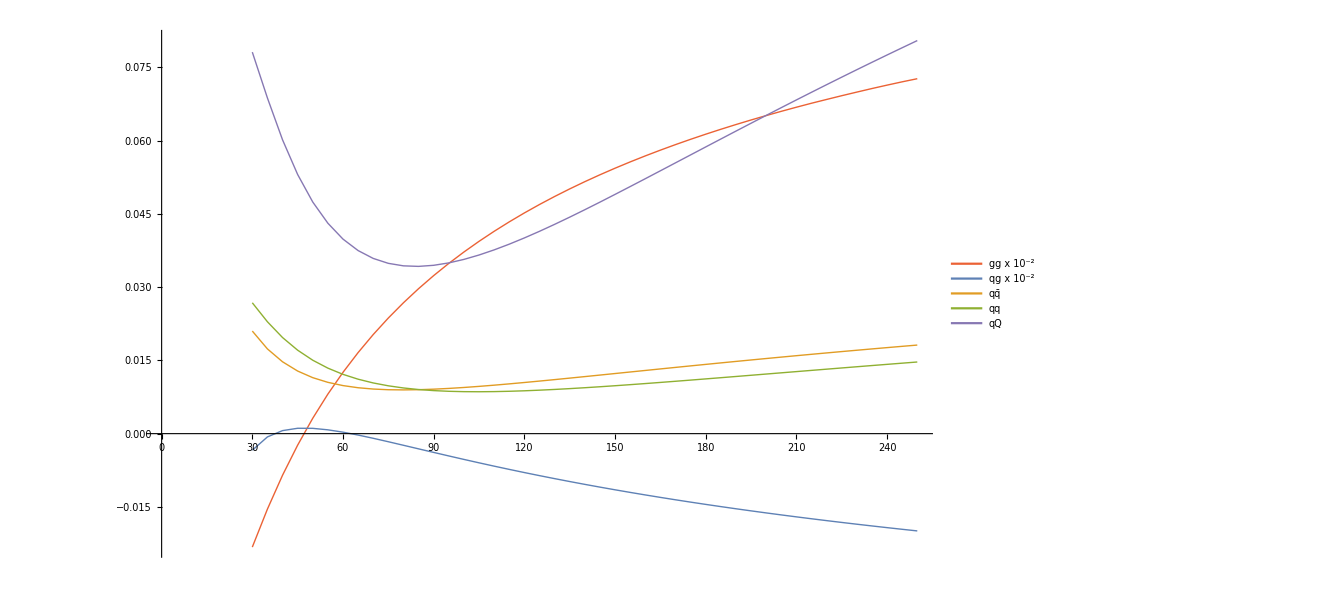

```mathematica
pp=ListLinePlot[Transpose[{Table[scales[[i]],{i,1,Length[scales]}],#}]&/@
({vars[[;;,1,4]]/100,vars[[;;,2,4]]/100,vars[[;;,3,4]],vars[[;;,4,4]],vars[[;;,5,4]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[5]],Thick},
{ColorData[97,"ColorList"][[6]],Thick}
},
PlotLegends->Placed[LineLegend[{"gg x 10^-2 ","qg x 10^-2 \t","qq̄\t","qq\t","qQ"},LegendLayout->{"Row",3}],{0.8,0.6}]
]
```

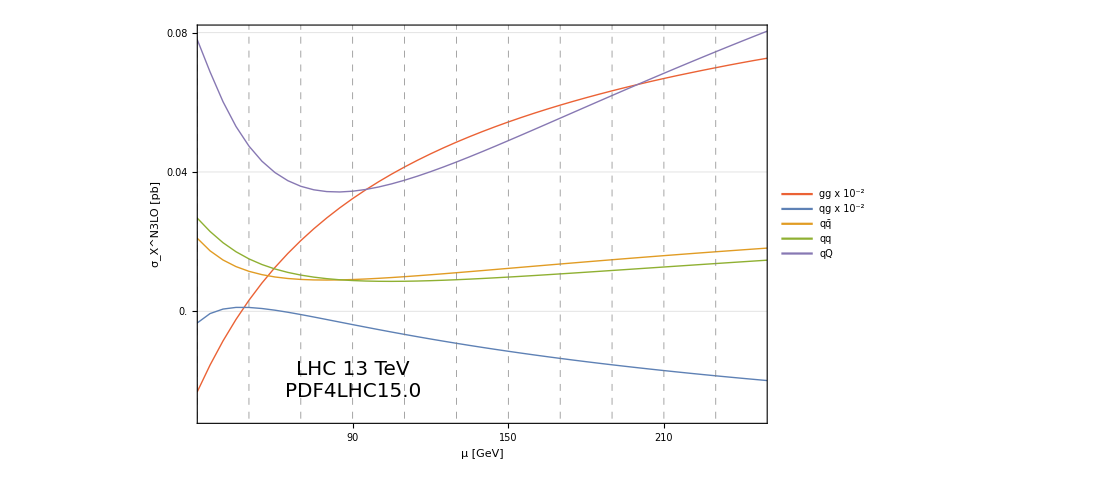

```mathematica
Show[pp,
PlotRange->{{34.3,245.6},{-0.03,0.08}},
Frame->True,
FrameTicks->{Table[{10+20 i ,10+i 20 },{i,1,25}],2/1000 Table[{10i,10i}//N,{i,-10,10}],None,None},
GridLines->{Table[{10+20 i ,10+i 20 },{i,1,30}],2/1000 Table[{10i,10i}//N,{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"μ [GeV]","σ_X^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0",20],{90,-0.02}]
]
```

## Truncation Order

```mathematica
vars=StringReplace[Import["Distributions/ThresholdExpansion.txt"],{"e-"->"*10^-"}]//ToExpression;
```

```mathematica
gg=vars[[;;,1,4]];
qg=vars[[;;,2,4]];
qqbar=vars[[;;,3,4]];
qq=vars[[;;,4,4]];
qQ2=vars[[;;,5,4]];
tot=gg+qg+qqbar+qq+qQ2
```

{-0.296109,2.85596,2.77444,2.60562,2.0186,2.07689,2.10131,2.10823,2.10917,2.10869,2.10794,2.10726,2.10686,2.10673,2.10686,2.10721,2.10772,2.10838,2.10914,2.10999,2.1109,2.11187,2.11285,2.11387,2.1149,2.11595,2.11699,2.11803,2.11906,2.12008,2.12111,2.1221,2.12309,2.12406,2.12501,2.12594,2.12685,2.12776,2.12862,2.12949,2.13033,2.13118,2.13197,2.13276,2.13353,2.13428,2.13502,2.13575,2.13645,2.13714,2.13782}

```mathematica
exact={2.82689,-0.695564,0.00874604,0.00743775,0.0360529,Total[{2.82689,-0.695564,0.00874604,0.00743775,0.0360529}]};
exact2=Table[exact,{i,1,Length[gg]}];
%%//Total
```

4.36713

### gg

```mathematica
gg//Length
```

51

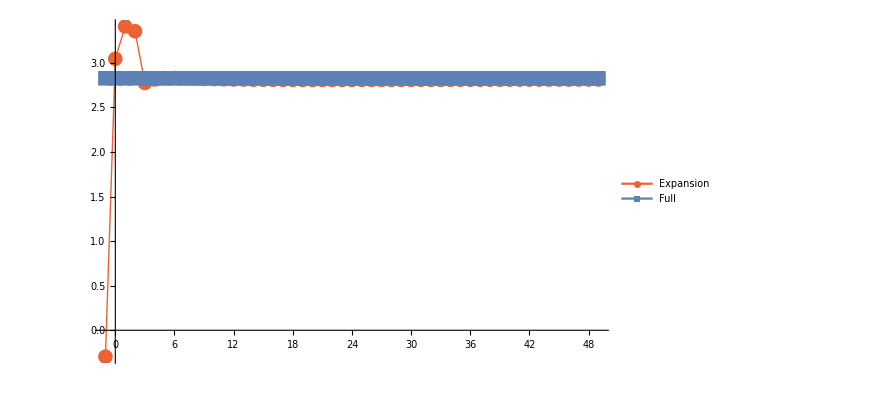

```mathematica
pp=ListLinePlot[Transpose[{Table[i,{i,-1,49}],#}]&/@
({gg,exact2[[;;,1]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.5}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

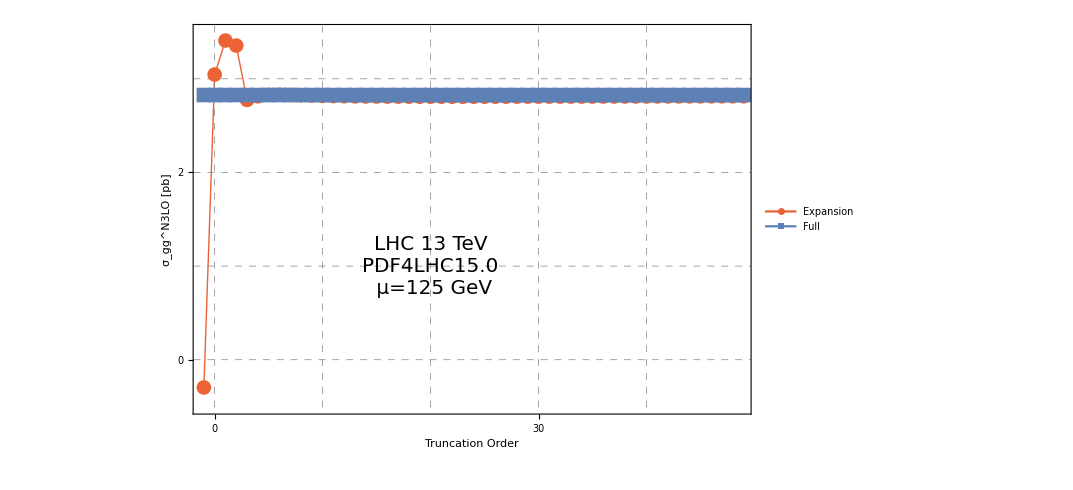

```mathematica
Show[pp,
PlotRange->{{-1,48.7},{-0.5,3.5}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i},{i,-10,10}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i},{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_gg^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{20,1}]
]
```

### qg

```mathematica
gg//Length
```

51

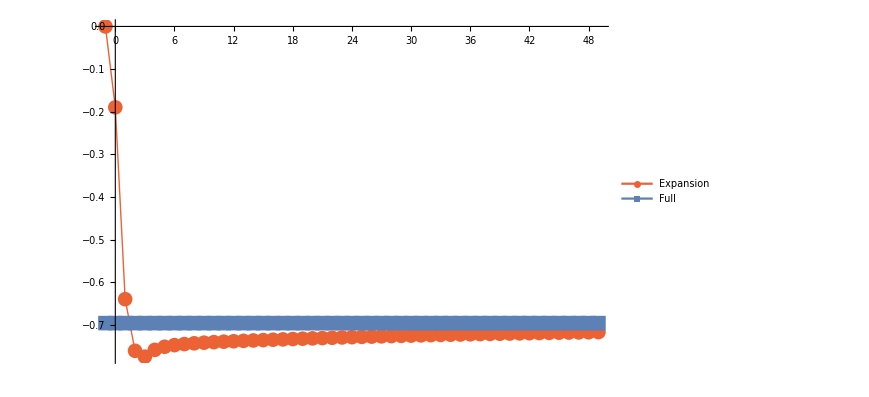

```mathematica
pp=ListLinePlot[Transpose[{Table[i,{i,-1,49}],#}]&/@
({qg,exact2[[;;,2]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.5}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

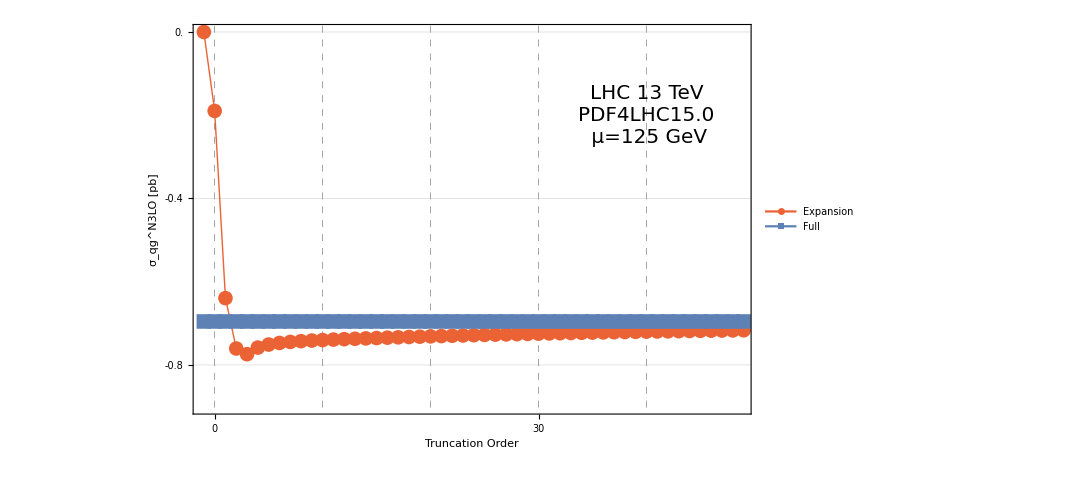

```mathematica
Show[pp,
PlotRange->{{-1,48.7},{-0.9,0}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{i,i}2/10//N,{i,-10,10}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{i,i}2/10//N,{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_qg^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,-0.2}]
]
```

### qqbar

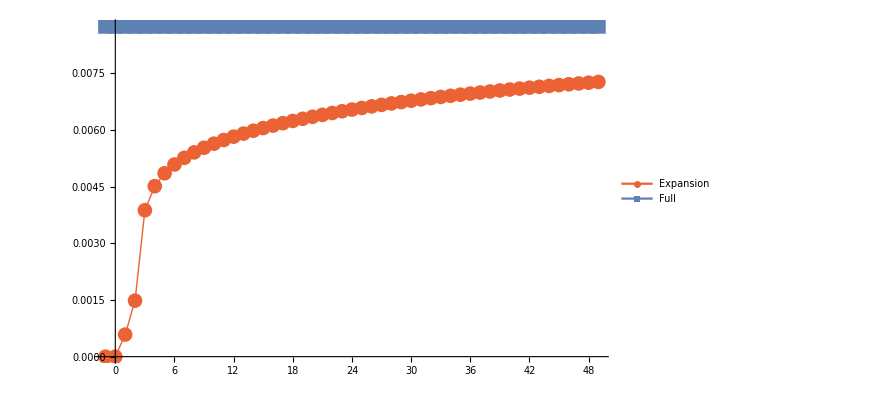

```mathematica
pp=ListLinePlot[Transpose[{Table[i,{i,-1,49}],#}]&/@
({qqbar,exact2[[;;,3]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.5}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

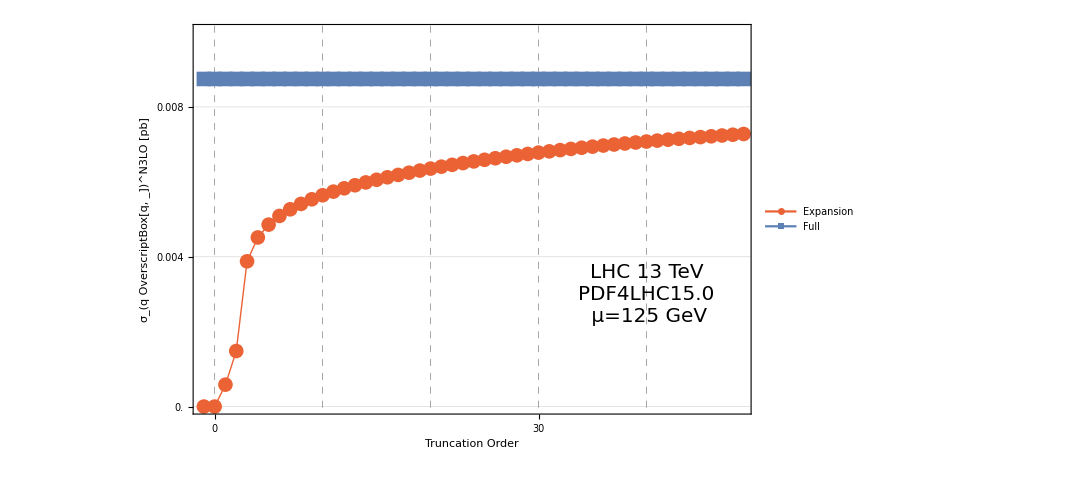

```mathematica
Show[pp,
PlotRange->{{-1,48.7},{0,0.01}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{i,i}2/1000//N,{i,-10,10}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{i,i}2/1000//N,{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_(q OverscriptBox[q, _])^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,0.003}]
]
```

### qq

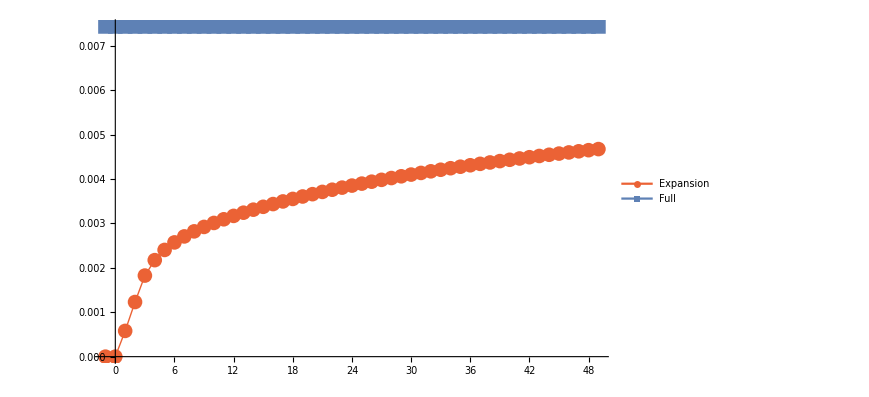

```mathematica
pp=ListLinePlot[Transpose[{Table[i,{i,-1,49}],#}]&/@
({qq,exact2[[;;,4]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.7}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

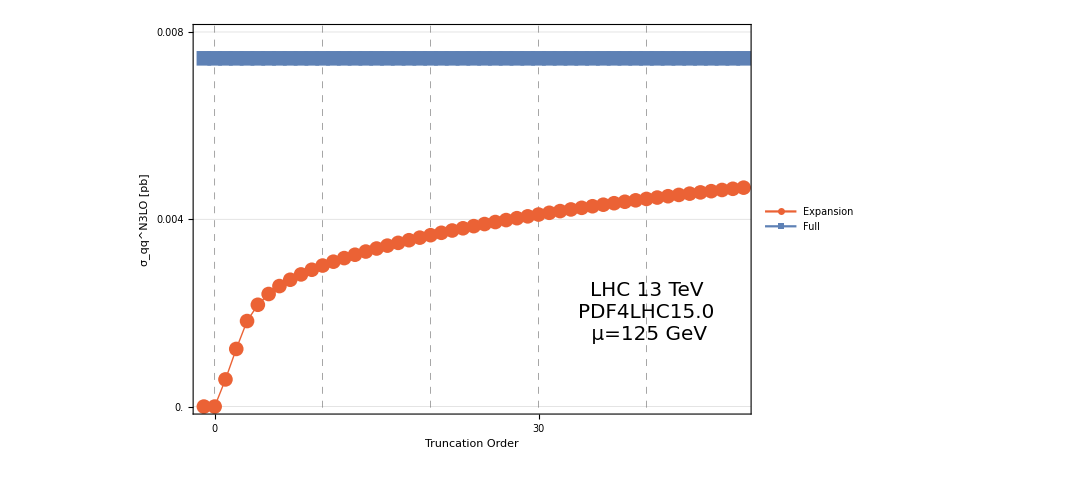

```mathematica
Show[pp,
PlotRange->{{-1,48.7},{0,0.008}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{i,i}2/1000//N,{i,-10,10}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{i,i}2/1000//N,{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_qq^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,0.002}]
]
```

### qQ2

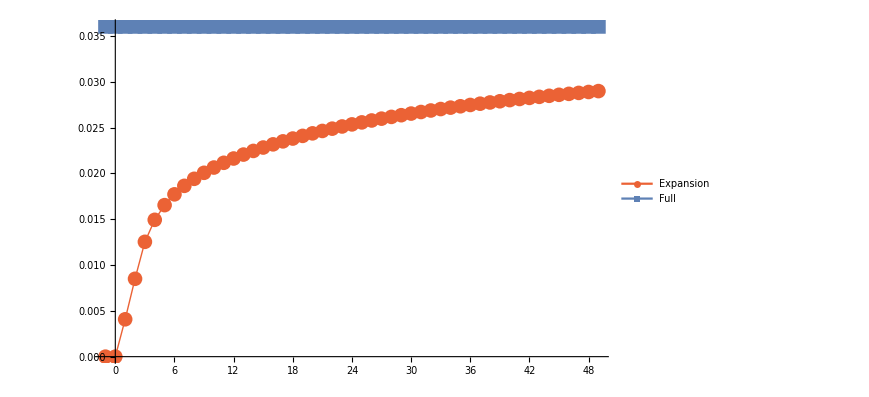

```mathematica
pp=ListLinePlot[Transpose[{Table[i,{i,-1,49}],#}]&/@
({qQ2,exact2[[;;,5]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.5}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

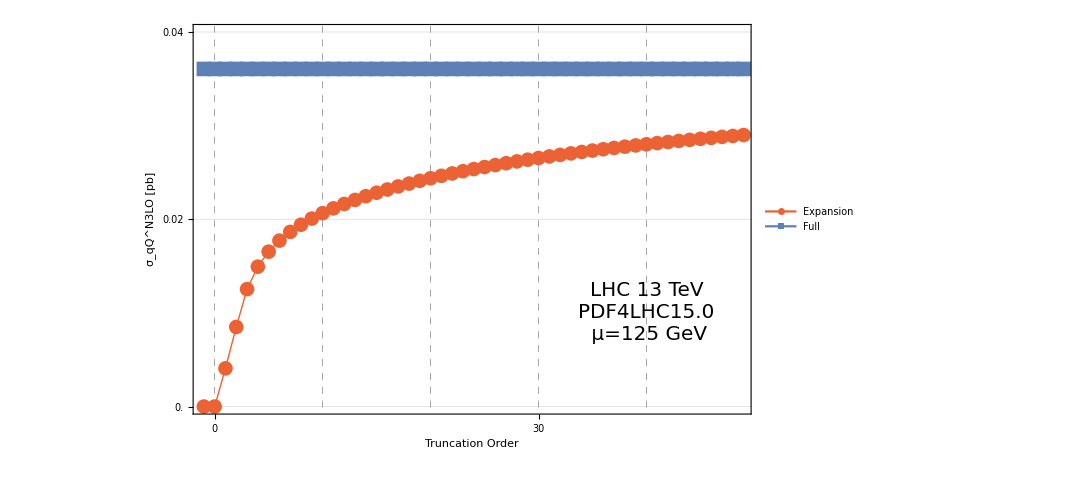

```mathematica
Show[pp,
PlotRange->{{-1,48.7},{0,0.04}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{i,i}10/1000//N,{i,-10,10}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{i,i}10/1000//N,{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_qQ^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,0.01}]
]
```

### tot

```mathematica
gg//Length
```

51

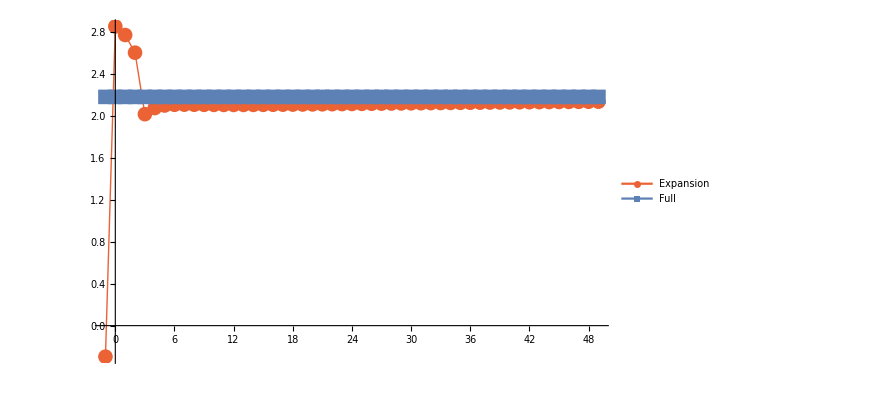

```mathematica
pp=ListLinePlot[Transpose[{Table[i,{i,-1,49}],#}]&/@
({tot,exact2[[;;,6]]})

,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.5}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

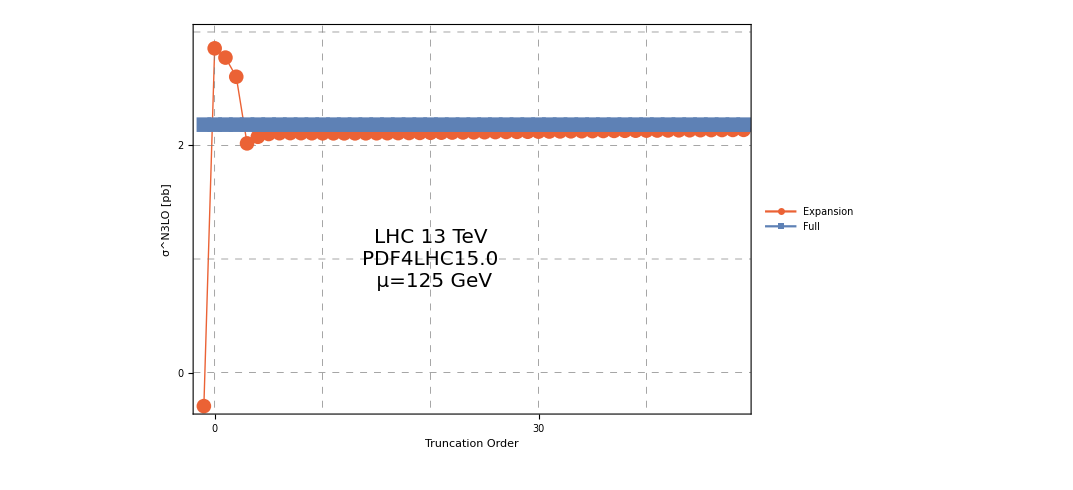

```mathematica
Show[pp,
PlotRange->{{-1,48.7},{-0.3,3.0}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i},{i,-10,10}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i},{i,-10,10}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ^N3LO [pb]"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{20,1}]
]
```

## Truncation Order Relative

```mathematica
vars=StringReplace[Import["Distributions/ThresholdExpansion.txt"],{"e-"->"*10^-"}]//ToExpression;
```

```mathematica
gg=vars[[;;,1,4]];
qg=vars[[;;,2,4]];
qqbar=vars[[;;,3,4]];
qq=vars[[;;,4,4]];
qQ2=vars[[;;,5,4]];
tot=gg+qg+qqbar+qq+qQ2
```

{-0.296109,2.85596,2.77444,2.60562,2.0186,2.07689,2.10131,2.10823,2.10917,2.10869,2.10794,2.10726,2.10686,2.10673,2.10686,2.10721,2.10772,2.10838,2.10914,2.10999,2.1109,2.11187,2.11285,2.11387,2.1149,2.11595,2.11699,2.11803,2.11906,2.12008,2.12111,2.1221,2.12309,2.12406,2.12501,2.12594,2.12685,2.12776,2.12862,2.12949,2.13033,2.13118,2.13197,2.13276,2.13353,2.13428,2.13502,2.13575,2.13645,2.13714,2.13782}

```mathematica
exact={2.82689,-0.695564,0.00874604,0.00743775,0.0360529,Total[{2.82689,-0.695564,0.00874604,0.00743775,0.0360529}]};
exact2=Table[exact,{i,1,Length[gg]}];
%%//Total
```

4.36713

```mathematica
qg
```

{-4.39506×10^-27,-0.189661,-0.639435,-0.760496,-0.774196,-0.758302,-0.751051,-0.747153,-0.744702,-0.742903,-0.741428,-0.740199,-0.739098,-0.738091,-0.737143,-0.736231,-0.735362,-0.734503,-0.733668,-0.732886,-0.732089,-0.731329,-0.730594,-0.729879,-0.729188,-0.72852,-0.727855,-0.727225,-0.726632,-0.726043,-0.725453,-0.724872,-0.724345,-0.723783,-0.723274,-0.722765,-0.7223,-0.721816,-0.721363,-0.720916,-0.720471,-0.720021,-0.719617,-0.719221,-0.718825,-0.718457,-0.71809,-0.717718,-0.71737,-0.717016,-0.71668}

### gg

```mathematica
gg//Length
```

51

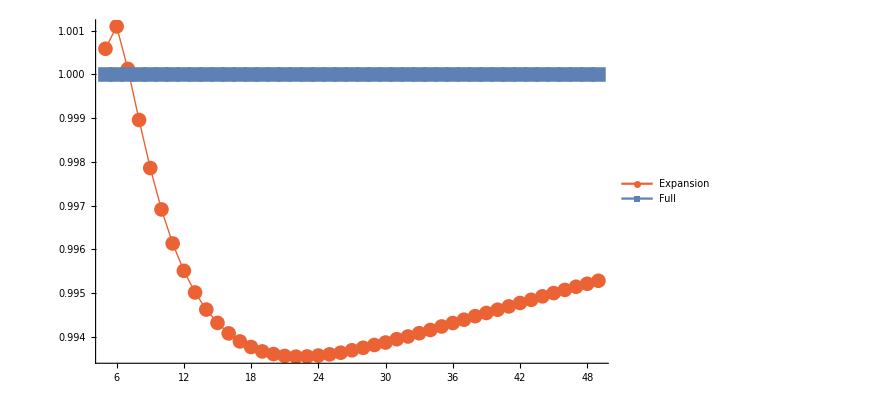

```mathematica
pp=ListLinePlot[
(Transpose[{Table[i,{i,-1,49}],#}]&/@
({gg/exact2[[;;,1]],Table[1,{i,1,Length[gg]}]}))[[;;,7;;]]
,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.5}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

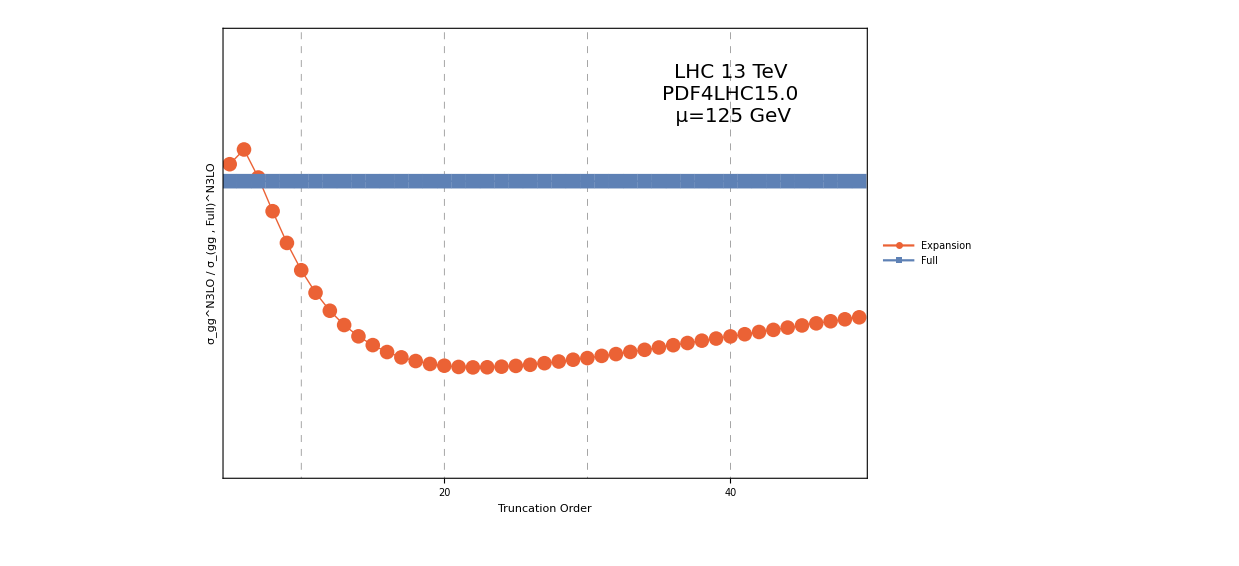

```mathematica
Show[pp,
PlotRange->{{5.4,48.7},{0.99,1.005}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i}/200//N,{i,99,300}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i}/200//N,{i,99,300}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_gg^N3LO / σ_(gg ,  Full)^N3LO"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,1.003}]
]
```

### qg

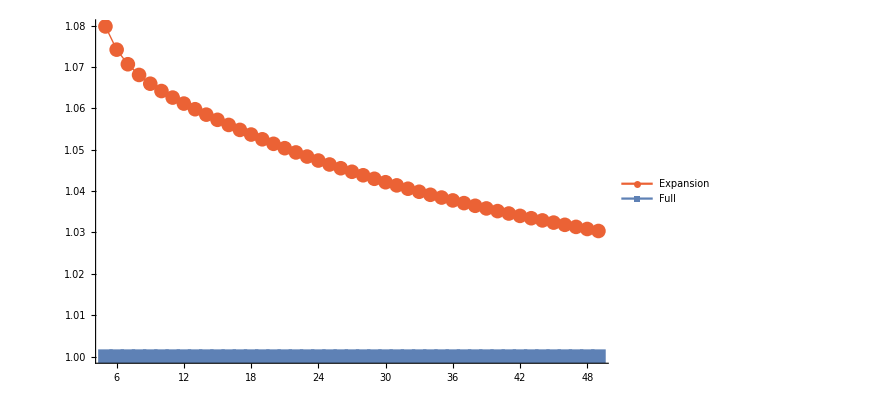

```mathematica
pp=ListLinePlot[
(Transpose[{Table[i,{i,-1,49}],#}]&/@
({qg/exact2[[;;,2]],Table[1,{i,1,Length[gg]}]}))[[;;,7;;]]
,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.7}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

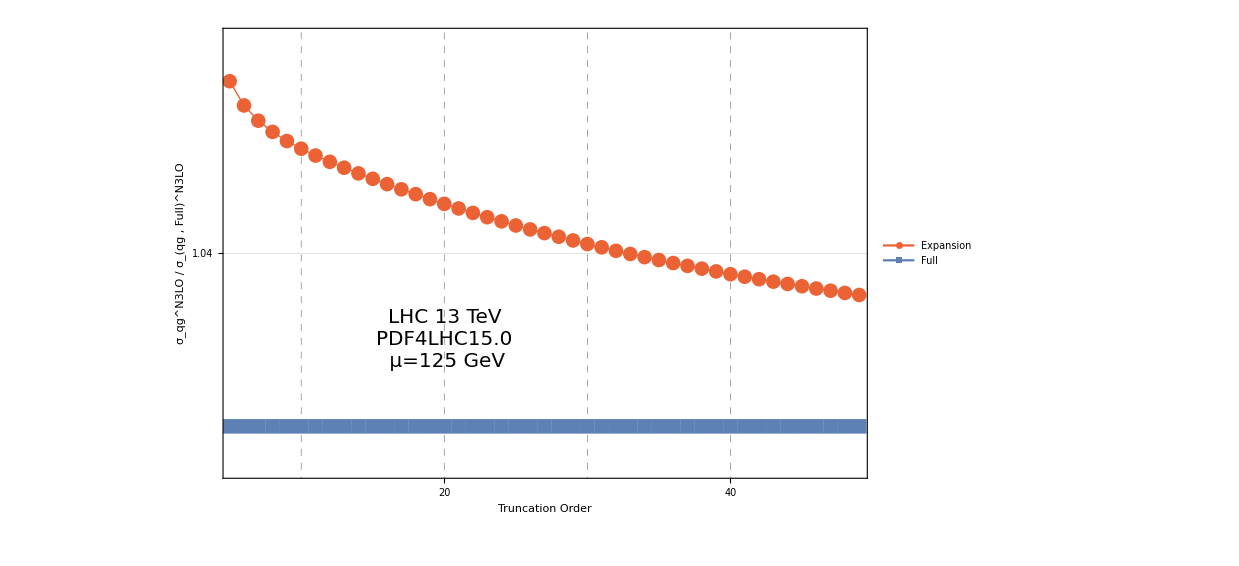

```mathematica
Show[pp,
PlotRange->{{5.4,48.7},{0.99,1.09}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i}/50//N,{i,40,300}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i}/50//N,{i,40,300}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_qg^N3LO / σ_(qg ,  Full)^N3LO"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{20,1.02}]
]
```

```mathematica
3
```

3

### qqbar

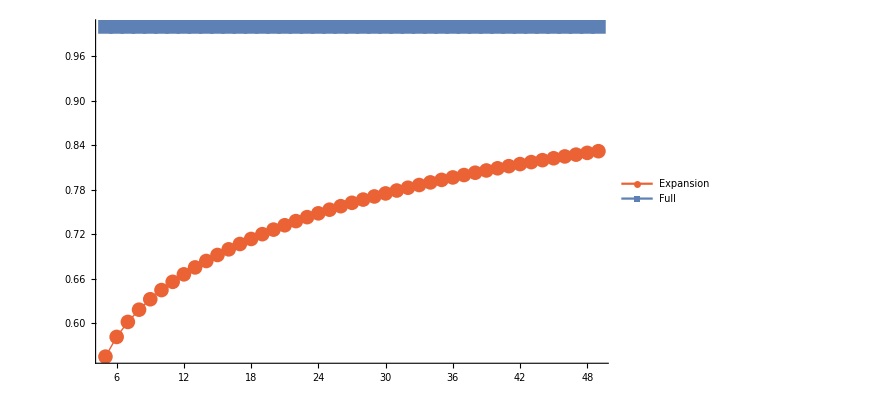

```mathematica
pp=ListLinePlot[
(Transpose[{Table[i,{i,-1,49}],#}]&/@
({qqbar/exact2[[;;,3]],Table[1,{i,1,Length[gg]}]}))[[;;,7;;]]
,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.7}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

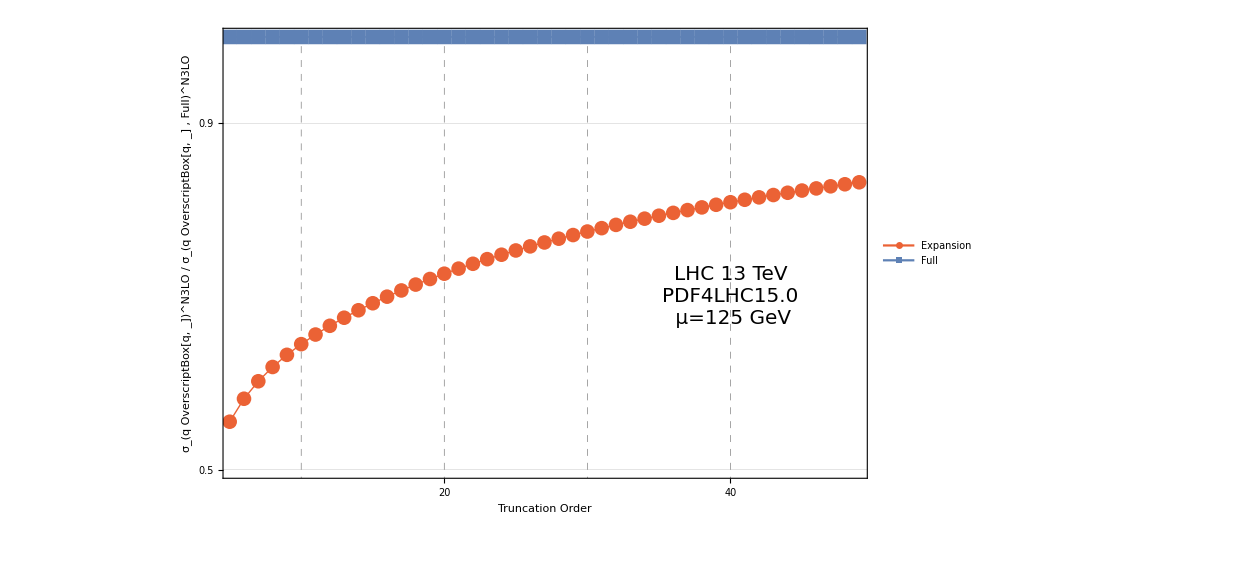

```mathematica
Show[pp,
PlotRange->{{5.4,48.7},{0.5,1}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i}/10//N,{i,1,300}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i}/10//N,{i,1,300}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_(q OverscriptBox[q, _])^N3LO / σ_(q OverscriptBox[q, _] ,  Full)^N3LO"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,0.7}]
]
```

```mathematica
3
```

3

### qq

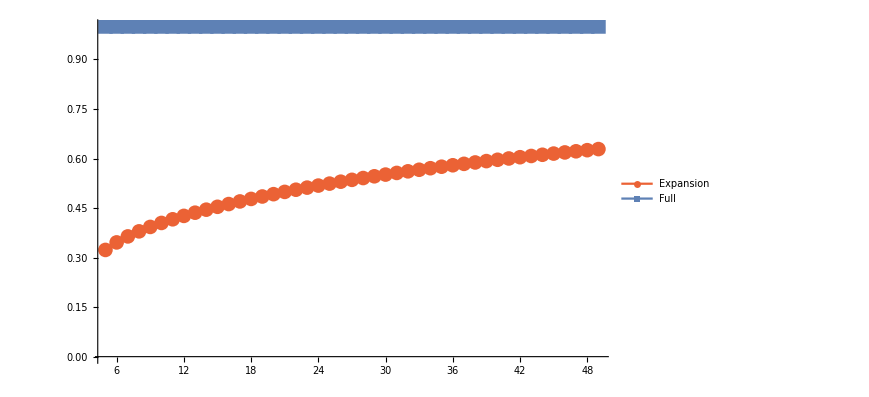

```mathematica
pp=ListLinePlot[
(Transpose[{Table[i,{i,-1,49}],#}]&/@
({qq/exact2[[;;,4]],Table[1,{i,1,Length[gg]}]}))[[;;,7;;]]
,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.7}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

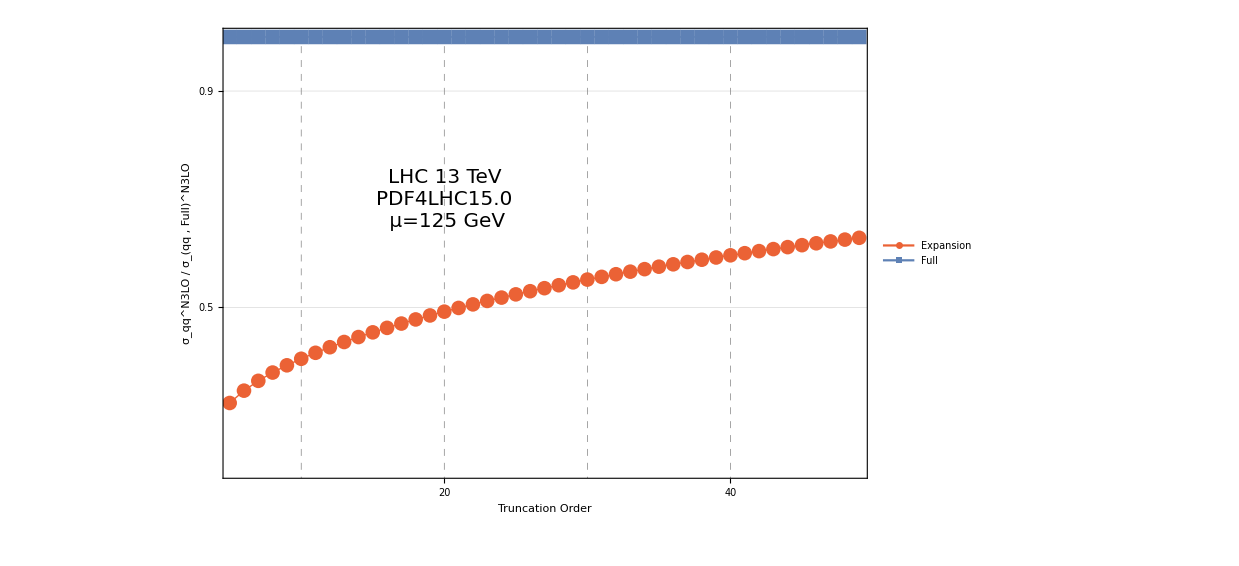

```mathematica
Show[pp,
PlotRange->{{5.4,48.7},{0.2,1}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i}/10//N,{i,1,300}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i}/10//N,{i,1,300}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_qq^N3LO / σ_(qq ,  Full)^N3LO"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{20,0.7}]
]
```

```mathematica
3
```

### qQ2

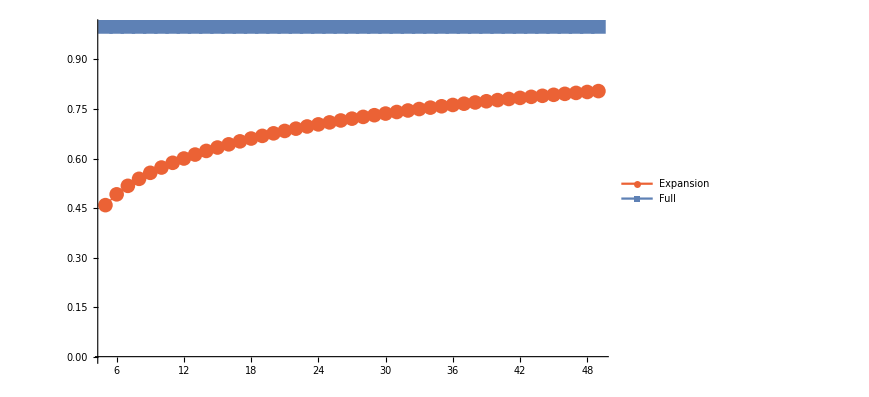

```mathematica
pp=ListLinePlot[
(Transpose[{Table[i,{i,-1,49}],#}]&/@
({qQ2/exact2[[;;,5]],Table[1,{i,1,Length[gg]}]}))[[;;,7;;]]
,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.7}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

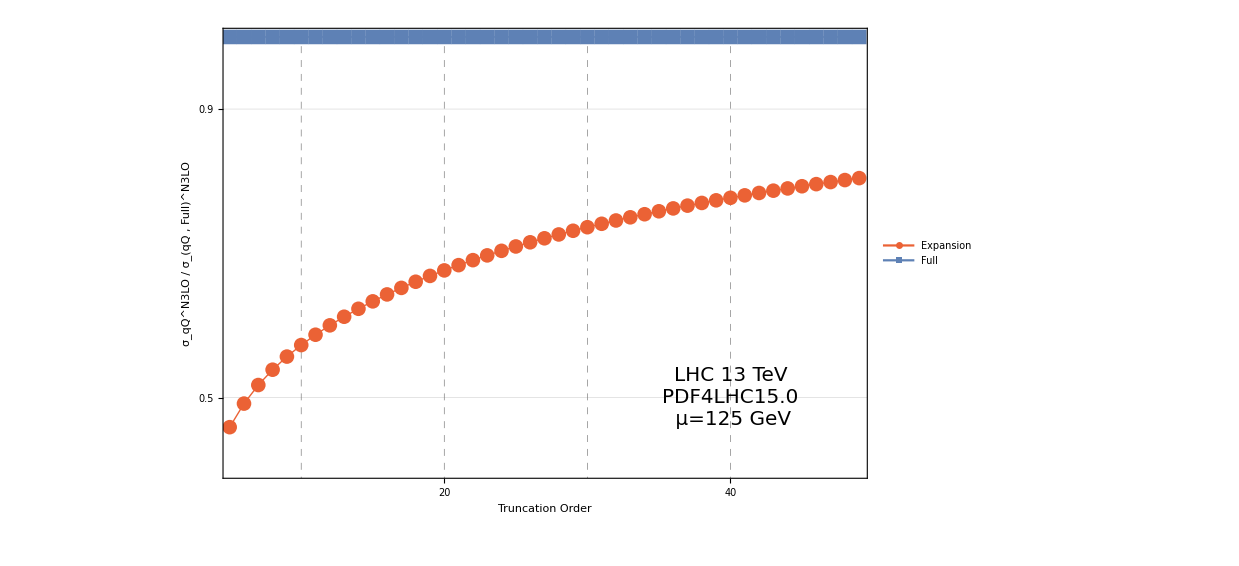

```mathematica
Show[pp,
PlotRange->{{5.4,48.7},{0.4,1}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i}/10//N,{i,1,300}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i}/10//N,{i,1,300}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_qQ^N3LO / σ_(qQ ,  Full)^N3LO"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,0.5}]
]
```

### tot

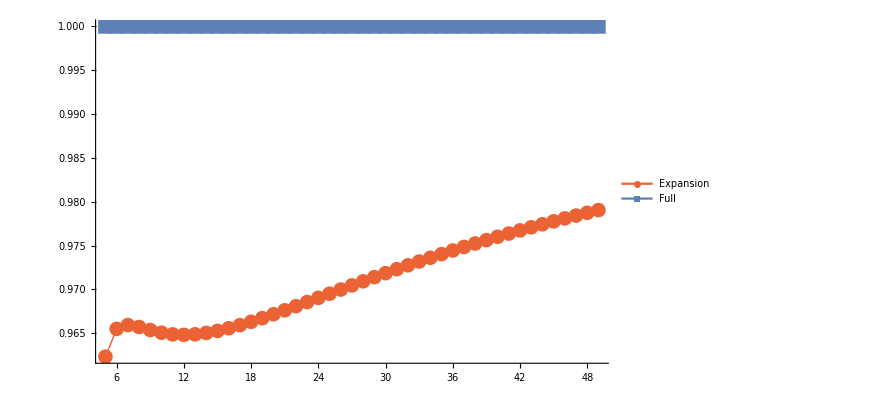

```mathematica
pp=ListLinePlot[
(Transpose[{Table[i,{i,-1,49}],#}]&/@
({tot/exact2[[;;,6]],Table[1,{i,1,Length[gg]}]}))[[;;,7;;]]
,PlotStyle->{{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
PlotLegends->Placed[LineLegend[{"Expansion\t     ","Full\t"},LegendLayout->{"Row",2}],{0.8,0.7}],
PlotMarkers->{Automatic,15},
PlotRange->All
]
```

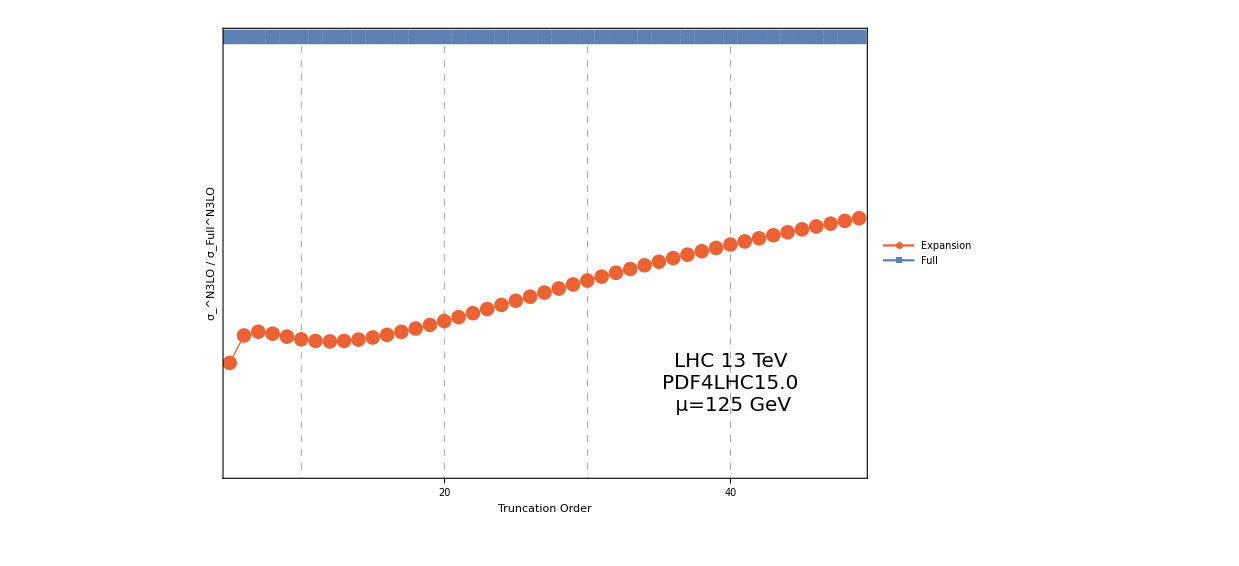

```mathematica
Show[pp,
PlotRange->{{5.4,48.7},{0.95,1}},
Frame->True,
FrameTicks->{Table[{-10+10 i ,-10+i 10 },{i,1,25}], Table[{1i,1i}/100//N,{i,1,300}],None,None},
GridLines->{Table[{-10+10 i ,-10+i 10 },{i,1,30}], Table[{1i,1i}/100//N,{i,1,300}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{"Truncation Order","σ_^N3LO / σ_Full^N3LO"},
LabelStyle->Directive[Bold,20],Epilog->Inset[Style["LHC 13 TeV\nPDF4LHC15.0\n μ=125 GeV",20],{40,0.96}]
]
```